```mathematica
Remove["Global`*"];
Unprotect[In,Out];
Clear[In,Out];
Off[General::spell1];
```

```mathematica
coords={t,r,θ,ϕ};
```

Define the metric

```mathematica
gdd={{g00,0,0,g03},{0,g11,0,0},{0,0,g22,0},{g03,0,0,g33}};
MatrixForm[gdd]
g00=(a^2 Sin[θ]^2-Δ[r])/ρ[r,θ];
g03=(Δ[r]-(r^2+a^2))a Sin[θ]^2/ρ[r,θ];
g11=ρ[r,θ]/Δ[r];
g22=ρ[r,θ];
g33=(-a^2 Δ[r] Sin[θ]^2+(r^2+a^2)^2)Sin[θ]^2/ρ[r,θ];MatrixForm[gdd]
```

(g00 | 0 | 0 | g03
0 | g11 | 0 | 0
0 | 0 | g22 | 0
g03 | 0 | 0 | g33)

((a^2 Sin[θ]^2-Δ[r])/ρ[r,θ] | 0 | 0 | (a Sin[θ]^2 (-a^2-r^2+Δ[r]))/ρ[r,θ]
0 | ρ[r,θ]/Δ[r] | 0 | 0
0 | 0 | ρ[r,θ] | 0
(a Sin[θ]^2 (-a^2-r^2+Δ[r]))/ρ[r,θ] | 0 | 0 | (Sin[θ]^2 ((a^2+r^2)^2-a^2 Sin[θ]^2 Δ[r]))/ρ[r,θ])

And its inverse and determinant

```mathematica
guu=Inverse[gdd];
dim=Length[gdd];
```

```mathematica
MatrixForm[guu]
```

((Sin[θ]^2 ((a^2+r^2)^2-a^2 Sin[θ]^2 Δ[r]) ρ[r,θ])/((-a^4 Sin[θ]^2-2 a^2 r^2 Sin[θ]^2-r^4 Sin[θ]^2+2 a^4 Sin[θ]^4+2 a^2 r^2 Sin[θ]^4-a^4 Sin[θ]^6) Δ[r]) | 0 | 0 | (-a Sin[θ]^2 ρ[r,θ]+(a^3 Sin[θ]^2 ρ[r,θ])/Δ[r]+(a r^2 Sin[θ]^2 ρ[r,θ])/Δ[r])/(-a^4 Sin[θ]^2-2 a^2 r^2 Sin[θ]^2-r^4 Sin[θ]^2+2 a^4 Sin[θ]^4+2 a^2 r^2 Sin[θ]^4-a^4 Sin[θ]^6)
0 | (-(a^4 Sin[θ]^2 Δ[r])/ρ[r,θ]-(2 a^2 r^2 Sin[θ]^2 Δ[r])/ρ[r,θ]-(r^4 Sin[θ]^2 Δ[r])/ρ[r,θ]+(2 a^4 Sin[θ]^4 Δ[r])/ρ[r,θ]+(2 a^2 r^2 Sin[θ]^4 Δ[r])/ρ[r,θ]-(a^4 Sin[θ]^6 Δ[r])/ρ[r,θ])/(-a^4 Sin[θ]^2-2 a^2 r^2 Sin[θ]^2-r^4 Sin[θ]^2+2 a^4 Sin[θ]^4+2 a^2 r^2 Sin[θ]^4-a^4 Sin[θ]^6) | 0 | 0
0 | 0 | (-(a^4 Sin[θ]^2)/ρ[r,θ]-(2 a^2 r^2 Sin[θ]^2)/ρ[r,θ]-(r^4 Sin[θ]^2)/ρ[r,θ]+(2 a^4 Sin[θ]^4)/ρ[r,θ]+(2 a^2 r^2 Sin[θ]^4)/ρ[r,θ]-(a^4 Sin[θ]^6)/ρ[r,θ])/(-a^4 Sin[θ]^2-2 a^2 r^2 Sin[θ]^2-r^4 Sin[θ]^2+2 a^4 Sin[θ]^4+2 a^2 r^2 Sin[θ]^4-a^4 Sin[θ]^6) | 0
-(a Sin[θ]^2 (-a^2-r^2+Δ[r]) ρ[r,θ])/((-a^4 Sin[θ]^2-2 a^2 r^2 Sin[θ]^2-r^4 Sin[θ]^2+2 a^4 Sin[θ]^4+2 a^2 r^2 Sin[θ]^4-a^4 Sin[θ]^6) Δ[r]) | 0 | 0 | (-ρ[r,θ]+(a^2 Sin[θ]^2 ρ[r,θ])/Δ[r])/(-a^4 Sin[θ]^2-2 a^2 r^2 Sin[θ]^2-r^4 Sin[θ]^2+2 a^4 Sin[θ]^4+2 a^2 r^2 Sin[θ]^4-a^4 Sin[θ]^6))

```mathematica
Do[g[i,j]=Simplify[gdd[[i,j]]];,{i,1,dim},{j,1,dim}];
Do[gu[i,j]=Simplify[guu[[i,j]]];,{i,1,dim},{j,1,dim}];
```

```mathematica
DET=Simplify[Det[gdd]];
```

Define the tetrad and its inverse

```mathematica
euu={{e00,0,0,e03},{0,e11,0,0},{0,0,e22,0},{e30,0,0,e33}};
```

```mathematica
(*we=0;*)(*Static observer*)
we=-g03/g33;(*Zero angular momentum observer*)
(*we=a/(r^2+a^2);*)(*Carter observer*)
(*we=Sqrt[M]/(r^(3/2)+Sqrt[M]a)*)(*Freely orbiting stationary observer*)
ut=1/Sqrt[-g00-2 g03 we-g33 we^2];
e00=ut;
e03=ut we;
e11=Sqrt[gu[2,2]];
e22=Sqrt[gu[3,3]];
e30=-Sqrt[ut^2+gu[1,1]];
e33=Sqrt[ut^2 we^2+gu[4,4]];
edd=Simplify[Inverse[euu],Csc[θ]>0&&r>0&&f2[r,θ]>0&&f1[r,θ]>0&&f0[r,θ]>0&&H[r]>0];
dim=Length[gdd];
```

```mathematica
Do[e[i,j]=edd[[i,j]];,{i,1,dim},{j,1,dim}];
```

```mathematica
Do[eu[i,j]=euu[[i,j]];,{i,1,dim},{j,1,dim}];
```

Define the electromagnetic potential

```mathematica
A=(Q r)/ρ[r,θ] {1,0,0,-a Sin[θ]^2};
MatrixForm[A]
```

((Q r)/ρ[r,θ]
0
0
-(a Q r Sin[θ]^2)/ρ[r,θ])

The electromagnetic tensor

```mathematica
F = Table[D[A[[ν]],coords[[μ]]] - D[A[[μ]],coords[[ν]]],{μ,1,dim},{ν,1,dim}];
MatrixForm[F];
```

and the EM tensor in the tetrad above

```mathematica
tetradF = Simplify[Table[Sum[F[[μ,ν]]euu[[b,μ]]euu[[c,ν]],{μ,1,dim},{ν,1,dim}],{b,1,dim},{c,1,dim}],Sin[θ]>0];
MatrixForm[tetradF]
```

(0 | (Q (a^2+r^2) √(((a^2+2 r^2+a^2 Cos[2 θ])^2 Δ[r])/(((a^2+r^2)^2-a^2 Sin[θ]^2 Δ[r]) ρ[r,θ])) (-ρ[r,θ]+r ρ^(1,0)[r,θ]))/((a^2+2 r^2+a^2 Cos[2 θ]) √(Δ[r]/ρ[r,θ]) ρ[r,θ]^2) | (Q r √(1/ρ[r,θ]) √(((a^2+2 r^2+a^2 Cos[2 θ])^2 Δ[r])/(((a^2+r^2)^2-a^2 Sin[θ]^2 Δ[r]) ρ[r,θ])) (2 a^2 Sin[2 θ] (a^2+r^2-Δ[r]) ρ[r,θ]+(a^2+r^2) (a^2+2 r^2+a^2 Cos[2 θ]) ρ^(0,1)[r,θ]))/((a^2+2 r^2+a^2 Cos[2 θ])^2 Δ[r] ρ[r,θ]) | 0
(Q (a^2+r^2) √(((a^2+2 r^2+a^2 Cos[2 θ])^2 Δ[r])/(((a^2+r^2)^2-a^2 Sin[θ]^2 Δ[r]) ρ[r,θ])) (ρ[r,θ]-r ρ^(1,0)[r,θ]))/((a^2+2 r^2+a^2 Cos[2 θ]) √(Δ[r]/ρ[r,θ]) ρ[r,θ]^2) | 0 | 0 | -(a Q Sin[θ]^2 √(Δ[r]/ρ[r,θ]) √((Csc[θ]^4 ρ[r,θ])/((a^2+r^2)^2 Csc[θ]^2-a^2 Δ[r])) (ρ[r,θ]-r ρ^(1,0)[r,θ]))/ρ[r,θ]^2
-(Q r √(1/ρ[r,θ]) √(((a^2+2 r^2+a^2 Cos[2 θ])^2 Δ[r])/(((a^2+r^2)^2-a^2 Sin[θ]^2 Δ[r]) ρ[r,θ])) (2 a^2 Sin[2 θ] (a^2+r^2-Δ[r]) ρ[r,θ]+(a^2+r^2) (a^2+2 r^2+a^2 Cos[2 θ]) ρ^(0,1)[r,θ]))/((a^2+2 r^2+a^2 Cos[2 θ])^2 Δ[r] ρ[r,θ]) | 0 | 0 | -a Q r Sin[θ] (1/ρ[r,θ])^(5/2) √((Csc[θ]^4 ρ[r,θ])/((a^2+r^2)^2 Csc[θ]^2-a^2 Δ[r])) (2 Cos[θ] ρ[r,θ]-Sin[θ] ρ^(0,1)[r,θ])
0 | (a Q Sin[θ]^2 √(Δ[r]/ρ[r,θ]) √((Csc[θ]^4 ρ[r,θ])/((a^2+r^2)^2 Csc[θ]^2-a^2 Δ[r])) (ρ[r,θ]-r ρ^(1,0)[r,θ]))/ρ[r,θ]^2 | a Q r Sin[θ] (1/ρ[r,θ])^(5/2) √((Csc[θ]^4 ρ[r,θ])/((a^2+r^2)^2 Csc[θ]^2-a^2 Δ[r])) (2 Cos[θ] ρ[r,θ]-Sin[θ] ρ^(0,1)[r,θ]) | 0)

Split it into the electric and magnetic fields

```mathematica
(*e1[r_,θ_] = Simplify[Re[tetradF[[1,2]]],r>0&&Sin[θ]>0&&Csc[θ]>0];
e2[r_,θ_] = Simplify[Re[tetradF[[1,3]]],r>0&&Sin[θ]>0&&Csc[θ]>0];
e3[r_,θ_] = Simplify[Re[tetradF[[1,4]]],r>0&&Sin[θ]>0&&Csc[θ]>0];
b1[r_,θ_] = Simplify[Re[tetradF[[4,3]]],r>0&&Sin[θ]>0&&Csc[θ]>0];
b2[r_,θ_] = Simplify[Re[tetradF[[2,4]]],r>0&&Sin[θ]>0&&Csc[θ]>0];
b3[r_,θ_] = Simplify[Re[tetradF[[3,2]]],r>0&&Sin[θ]>0&&Csc[θ]>0];*)
```

```mathematica
e1[r_,θ_] = Simplify[Re[F[[1,2]]],r>0&&Sin[θ]>0&&Csc[θ]>0];
e2[r_,θ_] = Simplify[Re[F[[1,3]]],r>0&&Sin[θ]>0&&Csc[θ]>0];
e3[r_,θ_] = Simplify[Re[F[[1,4]]],r>0&&Sin[θ]>0&&Csc[θ]>0];
b1[r_,θ_] = Simplify[Re[F[[4,3]]],r>0&&Sin[θ]>0&&Csc[θ]>0];
b2[r_,θ_] = Simplify[Re[F[[2,4]]],r>0&&Sin[θ]>0&&Csc[θ]>0];
b3[r_,θ_] = Simplify[Re[F[[3,2]]],r>0&&Sin[θ]>0&&Csc[θ]>0];
```

```mathematica
Δ[r_]:=r^2-2M r +a^2+ Q^2;
ρ[r_,θ_]:=r^2+a^2 Cos[θ]^2;
```

```mathematica
(*M=0;a=0;*)
```

Coordinate transformations from the tetrad coordinates to Cartesian coordinates

```mathematica
x[r_,θ_,ϕ_]:=r Sin[θ] Cos[ϕ]
y[r_,θ_,ϕ_]:=r Sin[θ] Sin[ϕ]
z[r_,θ_,ϕ_]:=r Cos[θ]
```

Standard rules for transforming a vector field from spherical coordinates to Carteisan coordinates
https://en.wikipedia.org/wiki/Vector_fields_in_cylindrical_and_spherical_coordinates#Spherical_coordinate_system

```mathematica
ex[r_,θ_,ϕ_]:=e1[r,θ] Sin[θ] Cos[ϕ]+e2[r,θ] Cos[θ] Cos[ϕ]-e3[r,θ] Sin[ϕ]
ey[r_,θ_,ϕ_]:=e1[r,θ] Sin[θ] Sin[ϕ]+e2[r,θ] Cos[θ] Sin[ϕ]+e3[r,θ] Cos[ϕ]
ez[r_,θ_,ϕ_]:=e1[r,θ] Cos[θ]-e2[r,θ] Sin[θ]
```

```mathematica
bx[r_,θ_,ϕ_]:=b1[r,θ] Sin[θ] Cos[ϕ]+b2[r,θ] Cos[θ] Cos[ϕ]-b3[r,θ] Sin[ϕ]
by[r_,θ_,ϕ_]:=b1[r,θ] Sin[θ] Sin[ϕ]+b2[r,θ] Cos[θ] Sin[ϕ]+b3[r,θ] Cos[ϕ]
bz[r_,θ_,ϕ_]:=b1[r,θ] Cos[θ]-b2[r,θ] Sin[θ]
```

```mathematica
M=1;
```

```mathematica
PlotYZEfield[aVal_,QVal_,n_]:=Block[{r,θ,ϕ=π/2,x=0,y,z,rh,rMax,a=aVal,Q=QVal},
If[Sqrt[a^2+Q^2]<M,
r[x_,y_,z_] := Sqrt[x^2+y^2+z^2];θ[x_,y_,z_] := ArcCos[z/r[x,y,z]];
rh := M+Sqrt[M^2-a^2-Q^2];
rMax=n rh;
YZey=Interpolation[Flatten[Table[{y,z,
Piecewise[{{ey[r[x,y,z],θ[x,y,z],ϕ],r[x,y,z]^2>(rh+0.01)^2}},0]
},{y,-rMax,rMax,rMax/100},{z,-rMax,rMax,rMax/100}],1],InterpolationOrder->1];
YZez=Interpolation[Flatten[Table[{y,z,
Piecewise[{{ez[r[x,y,z],θ[x,y,z],ϕ],r[x,y,z]^2>(rh+0.01)^2}},0]
},{y,-rMax,rMax,rMax/100},{z,-rMax,rMax,rMax/100}],1],InterpolationOrder->1];
YZe[y_,z_]=Sqrt[YZey[y,z]^2+YZez[y,z]^2];
DYZe[y_,z_]=D[YZe[y,z],{{y,z}}];
cP=ContourPlot[
Piecewise[{{YZe[Y,Z],Y^2+Z^2>(rh+0.01)^2}},0]
,{Y,-rMax,rMax},{Z,-rMax,rMax},Contours->8,ContourStyle->Red,ContourShading->Automatic,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->150,LegendMargins->{{-5,0},{-10,0}}],Right],ColorFunction->"Pastel",PlotLabel->"a="<>ToString[a]<>",Q="<>ToString[Q]];
sP=StreamPlot[
Piecewise[{{DYZe[Y,Z],Y^2+Z^2>(rh+0.01)^2}},{0,0}]
,{Y,-rMax,rMax},{Z,-rMax,rMax},StreamPoints->Coarse,StreamStyle->Blue];
Show[cP,sP,FrameLabel->{y,z}]]]
```

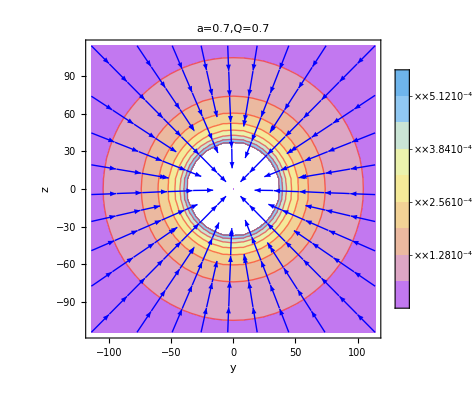

```mathematica
PlotYZEfield[0.7,0.7,100]
```

```mathematica
PlotYZBfield[aVal_,QVal_,n_]:=Block[{r,θ,ϕ=π/2,x=0,y,z,rh,rMax,a=aVal,Q=QVal},
If[Sqrt[a^2+Q^2]<M,
r[x_,y_,z_] := Sqrt[x^2+y^2+z^2];θ[x_,y_,z_] := ArcCos[z/r[x,y,z]];
rh := M+Sqrt[M^2-a^2-Q^2];
rMax=n rh;
YZby=Interpolation[Flatten[Table[{y,z,
Piecewise[{{by[r[x,y,z],θ[x,y,z],ϕ],r[x,y,z]^2>(rh+0.01)^2}},0]
},{y,-rMax,rMax,rMax/100},{z,-rMax,rMax,rMax/100}],1],InterpolationOrder->1];
YZbz=Interpolation[Flatten[Table[{y,z,
Piecewise[{{bz[r[x,y,z],θ[x,y,z],ϕ],r[x,y,z]^2>(rh+0.01)^2}},0]
},{y,-rMax,rMax,rMax/100},{z,-rMax,rMax,rMax/100}],1],InterpolationOrder->1];
YZb[y_,z_]=Sqrt[YZby[y,z]^2+YZbz[y,z]^2];
DYZb[y_,z_]=D[YZb[y,z],{{y,z}}];
cP=ContourPlot[
Piecewise[{{YZb[Y,Z],Y^2+Z^2>(rh+0.01)^2}},0]
,{Y,-rMax,rMax},{Z,-rMax,rMax},Contours->8,ContourStyle->Red,ContourShading->Automatic,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->150,LegendMargins->{{-5,0},{-10,0}}],Right],ColorFunction->"Pastel",PlotLabel->"a="<>ToString[a]<>",Q="<>ToString[Q]];
sP=StreamPlot[
Piecewise[{{DYZb[Y,Z],Y^2+Z^2>(rh+0.01)^2}},{0,0}]
,{Y,-rMax,rMax},{Z,-rMax,rMax},StreamPoints->Coarse,StreamStyle->Blue];
Show[cP,sP,FrameLabel->{y,z}]]]
```

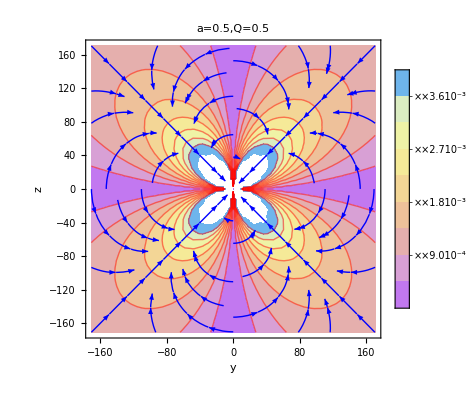

```mathematica
PlotYZBfield[0.5,0.5,100]
```

```mathematica
PlotXYEfield[aVal_,QVal_,n_]:=Block[{r,θ=π/2,ϕ,x,y,z=0,rh,rMax,a=aVal,Q=QVal},
If[Sqrt[a^2+Q^2]<M,
r[x_,y_,z_] := Sqrt[x^2+y^2+z^2];θ=π/2;ϕ[x_,y_,z_]:=ArcTan[y/x];
rh := M+Sqrt[M^2-a^2-Q^2];
rMax=n rh;
XYex=Interpolation[Flatten[Table[{x,y,
Piecewise[{{ex[r[x,y,z],θ,ϕ[x,y,z]],r[x,y,z]^2>(rh+0.01)^2&&x≠0}},0]
},{x,-rMax,rMax,rMax/100},{y,-rMax,rMax,rMax/100}],1],InterpolationOrder->1];
XYey=Interpolation[Flatten[Table[{x,y,
Piecewise[{{ey[r[x,y,z],θ,ϕ[x,y,z]],r[x,y,z]^2>(rh+0.01)^2&&x≠0}},0]
},{x,-rMax,rMax,rMax/100},{y,-rMax,rMax,rMax/100}],1],InterpolationOrder->1];
XYe[x_,y_]=Sqrt[XYex[x,y]^2+XYey[x,y]^2];
DXYe[x_,y_]=D[XYe[x,y],{{x,y}}];
cP=ContourPlot[
Piecewise[{{XYe[X,Y],X^2+Y^2>(rh+0.01)^2&&X≠0}},0]
,{X,-rMax,rMax},{Y,-rMax,rMax},Contours->8,ContourStyle->Red,ContourShading->Automatic,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->150,LegendMargins->{{-5,0},{-10,0}}],Right],ColorFunction->"Pastel",PlotLabel->"a="<>ToString[a]<>",Q="<>ToString[Q]];
sP=StreamPlot[
Piecewise[{{DXYe[X,Y],X^2+Y^2>(rh+0.01)^2&&X≠0}},{0,0}]
,{X,-rMax,rMax},{Y,-rMax,rMax},StreamPoints->Coarse,StreamStyle->Blue];
Show[cP,sP,FrameLabel->{x,y}]]]
```

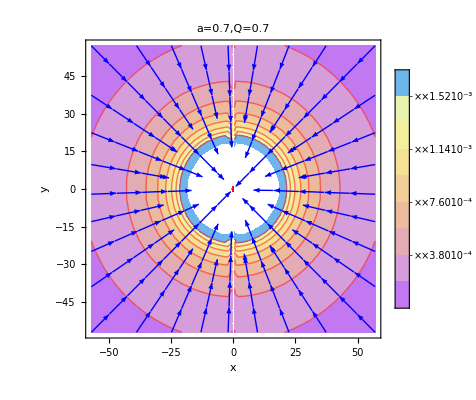

```mathematica
PlotXYEfield[0.7,0.7,50]
```

The magnetic field in the θ=π/2 plane is zero

```mathematica
Simplify[bx[r,π/2,0]]
by[r,π/2,0]
```

0

0

```mathematica
(*Export["YZE-Q=0.1.pdf",GraphicsGrid[ArrayReshape[Table[PlotYZEfield[a,0.1],{a,0.10,0.90,0.10}],{3,3}],ImageSize->850]];
Export["XYE-Q=0.1.pdf",GraphicsGrid[ArrayReshape[Table[PlotXYEfield[a,0.1],{a,0.10,0.90,0.10}],{3,3}],ImageSize->850]];
Export["XYE-Q=0.01.pdf",GraphicsGrid[ArrayReshape[Table[PlotXYEfield[a,0.01],{a,0.90,0.99,0.01}],{3,3}],ImageSize->850]];
Export["YZB-Q=0.1.pdf",GraphicsGrid[ArrayReshape[Table[PlotYZBfield[a,0.1],{a,0.10,0.90,0.10}],{3,3}],ImageSize->850]];
Export["YZB-Q=0.01.pdf",GraphicsGrid[ArrayReshape[Table[PlotYZBfield[a,0.01],{a,0.91,0.99,0.01}],{3,3}],ImageSize->850]];*)
```

```mathematica
Export["YZB-Q=0.1.pdf",GraphicsGrid[ArrayReshape[Table[PlotYZBfield[a,0.1,1000],{a,0.10,0.90,0.10}],{3,3}],ImageSize->850]];
```

$Aborted

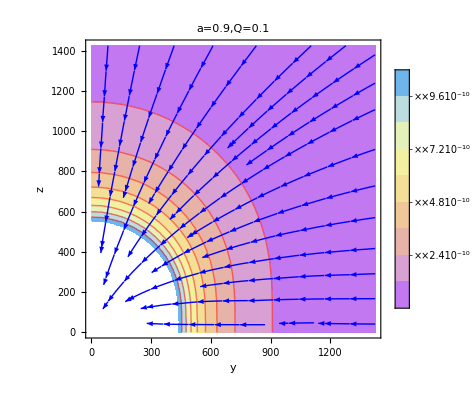

```mathematica
PlotYZBfield[0.9,0.1,1000]
```

```mathematica
n=2;
p1={PlotYZBfield[0.01,0.01,n],PlotYZBfield[0.5,0.01,n],PlotYZBfield[0.9,0.01,n],PlotYZBfield[0.99,0.01,n]};
p2={PlotYZEfield[0.01,0.01,n],PlotYZEfield[0.5,0.01,n],PlotYZEfield[0.9,0.01,n],PlotYZEfield[0.99,0.01,n]};
p3={PlotXYEfield[0.01,0.01,n],PlotXYEfield[0.5,0.01,n],PlotXYEfield[0.9,0.01,n],PlotXYEfield[0.99,0.01,n]};
```

InterpolatingFunction::dmval: Input value {0.294986, 0.294986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.294986, 0.294986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.294986, 0.294986} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
GraphicsGrid[{p1,p2,p3},ImageSize->1200,Spacings->{-50, -100}]
```

-Graphics-

```mathematica
n=5;
p1={PlotYZBfield[0.01,0.01,n],PlotYZBfield[0.5,0.01,n],PlotYZBfield[0.9,0.01,n],PlotYZBfield[0.99,0.01,n]};
p2={PlotYZEfield[0.01,0.01,n],PlotYZEfield[0.5,0.01,n],PlotYZEfield[0.9,0.01,n],PlotYZEfield[0.99,0.01,n]};
p3={PlotXYEfield[0.01,0.01,n],PlotXYEfield[0.5,0.01,n],PlotXYEfield[0.9,0.01,n],PlotXYEfield[0.99,0.01,n]};
```

InterpolatingFunction::dmval: Input value {0.723536, 0.723536} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.723536, 0.723536} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.723536, 0.723536} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
n
GraphicsGrid[{p1,p2,p3},ImageSize->1200,Spacings->{-50, -100}]
```

5

-Graphics-